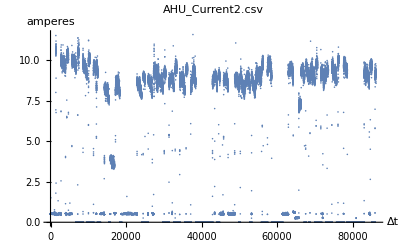

WeakStationarity:

True

Fitted time series model:

ARMAProcess[0.0247001,{0.123717,0.34381,0.199764,0.294591,0.218851,-0.186326},{0.7879,0.53244,0.388594,0.0982001,-0.112179,0.0587749},0.0742188]

CovarianceFunction::

Piecewise[{{19.5993 1.00218^(-1-Abs[s-t])-0.110289 2.20775^(-1-Abs[s-t])+0.000261818 0.806589^Abs[s-t] Cos[2.56828-2.66704 Abs[s-t]]+0.000751778 0.796034^Abs[s-t] Cos[1.30948-1.503 Abs[s-t]], Abs[s-t]>0}, {19.5302, True}}]

CorrelationFunction::

0.0512027 (Piecewise[{{19.5993 1.00218^(-1-Abs[s-t])-0.110289 2.20775^(-1-Abs[s-t])+0.000261818 0.806589^Abs[s-t] Cos[2.56828-2.66704 Abs[s-t]]+0.000751778 0.796034^Abs[s-t] Cos[1.30948-1.503 Abs[s-t]], Abs[s-t]>0}, {19.5302, True}}])

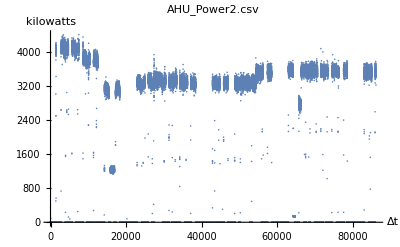

WeakStationarity:

True

Fitted time series model:

ARMAProcess[4.80902,{0.480402,0.427958,0.336058,-0.247341},{0.407192,0.102135,-0.187061,0.0642299},12239.7]

CovarianceFunction::

Piecewise[{{2.97337×10^6 1.00216^(-1-Abs[s-t])-13528.8 2.17236^(-1-Abs[s-t])+23.6213 0.733806^Abs[s-t] Cos[0.044847+2.29994 Abs[s-t]], Abs[s-t]>0}, {2.96394×10^6, True}}]

CorrelationFunction::

3.37388×10^-7 (Piecewise[{{2.97337×10^6 1.00216^(-1-Abs[s-t])-13528.8 2.17236^(-1-Abs[s-t])+23.6213 0.733806^Abs[s-t] Cos[0.044847+2.29994 Abs[s-t]], Abs[s-t]>0}, {2.96394×10^6, True}}])

Cross-Correlations::

{{{0.992299,0.989404},{0.989938,0.992567}},{{0.994343,0.991481},{0.991909,0.994587}},{{0.996252,0.993429},{0.99374,0.99647}},{{0.997885,0.995111},{0.995257,0.998062}},{{1.,0.997036},{0.997036,1.}},{{0.997885,0.995257},{0.995111,0.998062}},{{0.996252,0.99374},{0.993429,0.99647}},{{0.994343,0.991909},{0.991481,0.994587}},{{0.992299,0.989938},{0.989404,0.992567}}}

ignore::

{{Null^10},{□}}

```mathematica
{{ClearAll["Global`*"] 
(* https://www.wolfram.com/mathematica/new-in-10/expanded-time-series-processes/investigate-time-series-model-residuals.html *)
(* https://www.wolfram.com/mathematica/new-in-10/expanded-time-series-processes/vector-joint-model-versus-univariate-component-mod.html *)
(* Read individual files of 2 data columns each. *)
fitTimeseriesModel[f_,y_]:=Module[{fname=f,yaxis=y},
dataset=Import[StringJoin["/home/david/Documents/digital-twins/combed.iiitd/datasets/",fname],
{"CSV","Data",All,{1,2}},"HeaderLines"->1,"FieldSeparators"->",",MissingDataRules->{"."->Missing[],""->Missing[]}];
time=dataset[[All,1]];
time=Subtract[time,time[[1]]];
timeseries=TimeSeries[dataset[[All,2]],{time}]; (* is 2 because only 2 data columns read *)
 Print[ListPlot[dataset[[All,2]],PlotLabel->fname,AxesLabel->{"Δt",yaxis}]]; 
atsm=TimeSeriesModelFit[timeseries];
process=Normal[atsm];
Print["WeakStationarity:"];
Print[WeakStationarity[process]];
Print["Fitted time series model:"];
Print[process];
Print["CovarianceFunction::"];
cov=CovarianceFunction[process,s,t];
Print[cov];
Print["CorrelationFunction::"];
corr=CorrelationFunction[process,s,t];
Print[corr];
(*Print["cross-Correlation::"];
Print[%[[All,1,2]]];(* <<< *)
Print[Table[Show[atsm[plot,"LagMax"->20],ImageSize->200],{plot,{"ACFPlot","PACFPlot","LjungBoxPlot"}}]];*)
(* Print["ErrorVariance::"];
Print[atsm["ErrorVariance"]]; *)
(*Print[TimeSeriesForecast[process,dataset[[All,2]], 2]];*)
];
(***********************************************)
fitLinearTimeseriesModel[f_,y_]:=Module[{fname=f,yaxis=y},
dataset=Import[StringJoin["/home/david/Documents/digital-twins/combed.iiitd/datasets/",fname],
{"CSV","Data",All,{1,2}},"HeaderLines"->1,"FieldSeparators"->",",MissingDataRules->{"."->Missing[],""->Missing[]}];
time=dataset[[All,1]];
time=Subtract[time,time[[1]]];
timeseries=TimeSeries[dataset[[All,2]],{time}];
Print[ListPlot[dataset[[All,2]],PlotLabel->fname,AxesLabel->{"Time.offset",yaxis}]];
atsm=TimeSeriesModelFit[timeseries];
process=Normal[atsm];
Print[process];
model=LinearModelFit[timeseries,x,x];
Print["LinearModelFit::"];
Print[model["BestFit"]];
Show[ListPlot[timeseries],Plot[model["BestFit"],{x,0,300000}],Frame->True]
(*model["ParameterTable"];*)
];
(***********************************************)
xcorrlag[dat1_,dat2_]:=Position[#,Max@#]&[xcorr[dat1,dat2]]-Length[dat1]
xcorr[dat1_,dat2_]:=ListCorrelate[dat1,dat2,{-1,1},0]
xcorr[dat_]:=xcorr[dat,dat]
(***********************************************)
correlateTimeseriesModels[f1_,y1_,f2_,y2_]:=Module[{fname1=f1,yaxis1=y1,fname2=f2,yaxis2=y2},
dataset1=Import[StringJoin["/home/david/Documents/digital-twins/combed.iiitd/datasets/",fname1],
{"CSV","Data",All,{1,2}},"HeaderLines"->1,"FieldSeparators"->",",MissingDataRules->{"."->Missing[],""->Missing[]}];
dataset2=Import[StringJoin["/home/david/Documents/digital-twins/combed.iiitd/datasets/",fname2],
{"CSV","Data",All,{1,2}},"HeaderLines"->1,"FieldSeparators"->",",MissingDataRules->{"."->Missing[],""->Missing[]}];
time=dataset1[[All,1]];
time=Subtract[time,time[[1]]];
timeseries1=TimeSeries[dataset1[[All,2]],{time}]; 
timeseries2=TimeSeries[dataset2[[All,2]],{time}];  
corr=ListCorrelate[timeseries2["Values"],timeseries1["Values"],{-1,1},0];
lag=Position[#,Max@#]&[corr]-Length[timeseries1]; (* =86198 *)
temporalData=TemporalData[{Transpose[{timeseries2["Values"],timeseries1["Values"]}]},Automatic];
correlations=CorrelationFunction[temporalData,{-4,4}]["Values"];
Print["Cross-Correlations::"];
Print[correlations];
Print["ignore::"];
];
(***********************************************)
fitTimeseriesModel["AHU_Current2.csv","amperes"];
fitTimeseriesModel["AHU_Power2.csv","kilowatts"];
correlateTimeseriesModels["AHU_Current2.csv","amperes", "AHU_Power2.csv","kilowatts"];
(*fitLinearTimeseriesModel["AHU_Energy2.csv","EnergyUse"]; *)
(***********************************************)}, {□}}
```